## 130 Ba

```mathematica
ClearAll["Global`*"]
```

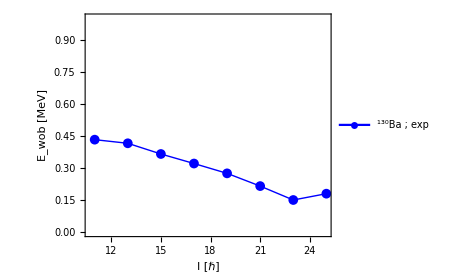

```mathematica
yrastEn=Sort[{11984.3,10821.3,9690.3,8574.3,7524.3,6563.3,5678.3,4884.2,4256.3,3790.3}];
wob1En=Sort[{10436.3,9283.3,8265.3,7319.3,6442.2,5647.2,4986.2,4456.2}];
yrastSpin=Table[i,{i,10,28,2}];
wob1Spin=Table[i,{i,11,25,2}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","130"],"Ba ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/130Ba.pdf",fig];
Show[fig]
```